# Packaged Food Ingredients

## Ingredients

Look up the raw ingredient list for a given food:

```mathematica
Entity["Food","VanDeKampsFilletsBeerBattered::rx25p"]["IngredientList"]
```

ALASKA POLLOCK, WATER, COTTONSEED OIL AND/OR SOYBEAN OIL, WHEAT FLOUR, YELLOW CORN FLOUR, WHEAT FLOUR (ENRICHED WITH NIACIN, FERROUS SULFATE, THIAMINE MONONITRATE, RIBOFLAVIN, FOLIC ACID), SALT, SOYBEAN OIL. CONTAINS 2% OR LESS OF: BEER (WATER, RICE, CORNSTARCH, BARLEY MALT, HOP EXTRACT, YEAST), MODIFIED FOOD STARCH, LEAVENING (SODIUM ACID PYROPHOSPHATE, SODIUM BICARBONATE, MONOCALCIUM PHOSPHATE), YEAST EXTRACT, SALT, SUGAR, DEXTROSE, SPICE, ONION POWDER, SODIUM TRIPOLYPHOSPHATE (TO RETAIN MOISTURE).

Get a computable list of ingredients:

```mathematica
Entity["Food","VanDeKampsFilletsBeerBattered::rx25p"]["Ingredients"]
```

{alaska pollock,water,cottonseed oil,soybean oil,wheat flour,yellow corn flour,salt,enriched with niacin,ferrous sulfate,thiamine mono-nitrate,riboflavin,folic acid,beer,modified food starch,leavening,yeast extract,sugar,dextrose,spice,onion powder,sodium tripolyphosphate,rice,cornstarch,barley malt,yeast,sodium acid pyrophosphate,sodium bicarbonate,monocalcium phosphate}

Find foods with a specific ingredient:

```mathematica
EntityValue[Entity["Food","Ingredients"->"OrangeExtract"],"Entities"]
```

{Ahold Pumpkin Cranberry Cracker Crisps,Drew's Dressing & Quick Marinade Harvest French,Holy-Mole Mole Sauce,Hot Cakes Bakery Scones Cranberry Orange - 3 CT,Little Miracles Organic Energy Lemongrass Tea,Little Miracles Organic Energy Lemongrass Tea Orange Juice Ginger Ginseng Agave,Maple Hill Creamery, Creamline Yogurt, Orange Creme,Polar Orange Juice Diet Orange Dry,Polar Orange Juice Diet Orange Dry,Polar Orange Juice Diet Orange Dry,Powell & Mahoney Cocktail Mixer Cosmopolitan,Powell & Mahoney Cocktail Mixer Margarita,Robert Rothschild Farm Organic Pineapple Habanero BBQ Gourmet Sauce,Robert Rothschild Farm Organic White Wine Creole Gourmet Sauce,Seattle, French Chocolate, Sorbets,Siggi's, 0% Milkfat Strained Non-Fat Yogurt, Orange & Ginger,Tait Farm Foods, Shrub Artisan Drink Mixer, Cranberry,The Great San Saba River Pecan Company Orange Pecan Marmalade}

Find foods with a specific set of ingredients:

```mathematica
EntityValue[Entity["Food","Ingredients"->ContainsAll[{"Rice","Beer"}]],"Entities"]
```

{Budweiser Hot Wing Sauce,Gorton's Beer Battered Fish Fillets,Gorton's Beer Battered Fish Tenders,Gorton's Classic Beer Battered Fish Fillets - 10 CT,Hungry-Man Pub Favorites Chicken Beer Battered,Hungry-Man Pub Favorites Grilled Beef Patty,Mrs. Paul's Fillets Beer Battered - 10 CT,Van de Kamp's Fillets Beer Battered}

Find foods without a specific ingredient:

```mathematica
EntityValue[,"Entities"]
```

{Casa Fiesta All Natural Spicy Refried Beans,Centrella Refried Beans,Ducal Refried Black Beans,Ducal Refried Red Beans,El Rio Refried Beans,Goya, Refried Pinto Beans With Chorizo,La Costena, Refried Black Beans,La Costena, Refried Pinto Beans,La Preferida, Inc. Refried Beans,La Preferida Refried Beans Fat Free,La Preferida Refried Beans Vegetarian,La Preferida, Refried Beans,La Preferida Refried Black Beans,Old El Paso Fat Free Refried Beans,Old El Paso Refried Beans Black Bean,Old El Paso Traditional Refried Beans,Old El Paso Vegetarian Refried Beans,Refried Pinto Beans Frijoles Bayos Refritos,San Francisco Frijoles Rojos Refried Black Beans,San Francisco Frijoles Rojos Refried Red Silk Beans,San Francisco, Refried Black Beans,San Francisco, Refried Black Beans,San Francisco, Refried Red Silk Beans,Taco Bell Home Originals Vegetarian Blend Refried Beans,Taco Bell Refried Beans Original,Traditional Refried Pinto Beans}

## Main Ingredients

Find only the top-level ingredients for a food:

```mathematica
Entity["Food","VanDeKampsFilletsBeerBattered::rx25p"]["MainIngredients"]
```

{alaska pollock,water,cottonseed oil,soybean oil,wheat flour,yellow corn flour,salt}

Find foods by top-level ingredients:

```mathematica
EntityValue[Entity["Food","MainIngredients"->"AlaskaPollock"],"Entities"]//Shallow
```

{American Pride Seafood, Beer Battered Wild Alaska Pollock Fillets,American Pride, Wild Alaska Pollock Fillets, Sea Salt & Pepper,American Pride, Wild Alaska Pollock Fish Sticks,American Pride, Wild Alaska Pollock Flaky Fillets With A Lemon Pepper Crust, Lemon Pepper,American Pride, Wild Alaska Pollock, Garlic & Herb,Chashu Tenpura, Fried Fish Cake With Sweet Pork,Chunk Style Deluxe Imitation Crab,Crab Classic Imitation Crab,Flake Style Imitation Crabmeat,Gobo Tenpura Fried Fish Cake With Burdock,«57»}

## Ingredient Counts

Find the number of ingredients that a food has:

```mathematica
Entity["Food","CrabClassicImitationCrab::44qr9"]["IngredientCount"]
```

31

Find foods with less than a certain number of ingredients:

```mathematica
EntityClass["Food",{"Variety"->"Saltine","FoodType"->"Cracker","IngredientCount"->LessThan[20]}]["IngredientCount","NonMissingEntityAssociation"]//Sort
```

<|Nabisco Original Premium Saltine Crackers→15,Premium Saltine Crackers Original→16,Premium Rounds Unsalted Tops Saltine Crackers→16,Nabisco Premium Saltine Crackers→16,Nabisco Premium Minis Original Saltine Crackers→16,Keebler Original Zesta Saltine Crackers→16,Nabisco Premium Rounds Saltine Crackers→17,Back To Nature Organic Crackers Classic Saltine→17,Premium Saltine Crackers with Whole Grain→18,Nabisco Premium Unsalted Tops Saltine Crackers→18,Nabisco Premium Fat Free Saltine Crackers→19|>

Analyze the number of ingredients in different breads:

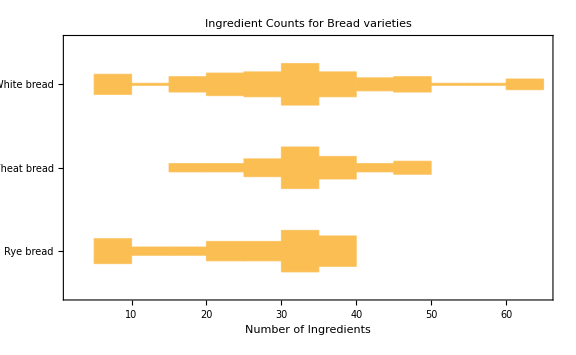

```mathematica
DistributionChart[
KeyValueMap[
Labeled[DeleteMissing[#2["IngredientCount"]],#1]&,
<|
"Rye bread" ->,
"Wheat bread"->,
"White bread"-> 
|>
],
BarOrigin->Left,
PlotLabel->Style["Ingredient Counts for Bread varieties",16],
FrameLabel->{"Number of Ingredients"},
ChartElementFunction->"HistogramDensity",
ImageSize->Large
]
```